```mathematica
Quit[]
```

```mathematica
Needs["FeynArts`"]
Needs["FormCalc`"]
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (11 Dec 2021)

by Thomas Hahn

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
SetOptions[InsertFields, Model -> ToFileName[NotebookDirectory[],"modelFiles/SMS-stop-NLO_FA/SMS-stop-NLO_FA"],GenericModel->ToFileName[NotebookDirectory[],"modelFiles/SMS-stop-NLO_FA/SMS-stop-NLO_FA"],ExcludeParticles->{S[1]}];
SetOptions[Paint, PaintLevel -> {Classes}];
```

```mathematica
M$ClassesDescription
```

{V[1]=={SelfConjugate→True,PropagatorType→Sine,PropagatorArrow→None,Mass→0,Indices→{},PropagatorLabel→A},V[2]=={SelfConjugate→True,PropagatorType→Sine,PropagatorArrow→None,Mass→MZ,Indices→{},PropagatorLabel→Z},V[3]=={SelfConjugate→False,QuantumNumbers→{Q},PropagatorType→Sine,PropagatorArrow→Forward,Mass→MW,Indices→{},PropagatorLabel→W},V[4]=={SelfConjugate→True,PropagatorType→Cycles,PropagatorArrow→None,Mass→0,Indices→{Index[Gluon]},PropagatorLabel→G},U[1]=={SelfConjugate→False,QuantumNumbers→{GhostNumber},PropagatorType→GhostDash,PropagatorArrow→Forward,Mass→0,Indices→{},PropagatorLabel→ghA},U[2]=={SelfConjugate→False,QuantumNumbers→{GhostNumber},PropagatorType→GhostDash,PropagatorArrow→Forward,Mass→MZ,Indices→{},PropagatorLabel→ghZ},U[3]=={SelfConjugate→False,QuantumNumbers→{GhostNumber,Q},PropagatorType→GhostDash,PropagatorArrow→Forward,Mass→MW,Indices→{},PropagatorLabel→ghWp},U[4]=={SelfConjugate→False,QuantumNumbers→{GhostNumber,-Q},PropagatorType→GhostDash,PropagatorArrow→Forward,Mass→MW,Indices→{},PropagatorLabel→ghWm},U[5]=={SelfConjugate→False,QuantumNumbers→{GhostNumber},PropagatorType→GhostDash,PropagatorArrow→Forward,Mass→0,Indices→{Index[Gluon]},PropagatorLabel→ghG},F[1]=={SelfConjugate→False,QuantumNumbers→{LeptonNumber},PropagatorType→Straight,PropagatorArrow→Forward,Mass→0,Indices→{},PropagatorLabel→ve},F[2]=={SelfConjugate→False,QuantumNumbers→{LeptonNumber},PropagatorType→Straight,PropagatorArrow→Forward,Mass→0,Indices→{},PropagatorLabel→vm},F[3]=={SelfConjugate→False,QuantumNumbers→{LeptonNumber},PropagatorType→Straight,PropagatorArrow→Forward,Mass→0,Indices→{},PropagatorLabel→vt},F[4]=={SelfConjugate→False,QuantumNumbers→{-Q,LeptonNumber},PropagatorType→Straight,PropagatorArrow→Forward,Mass→Me,Indices→{},PropagatorLabel→e},F[5]=={SelfConjugate→False,QuantumNumbers→{-Q,LeptonNumber},PropagatorType→Straight,PropagatorArrow→Forward,Mass→MMU,Indices→{},PropagatorLabel→mu},F[6]=={SelfConjugate→False,QuantumNumbers→{-Q,LeptonNumber},PropagatorType→Straight,PropagatorArrow→Forward,Mass→MTA,Indices→{},PropagatorLabel→ta},F[7]=={SelfConjugate→False,QuantumNumbers→{(2 Q)/3},PropagatorType→Straight,PropagatorArrow→Forward,Mass→MU,Indices→{Index[Colour]},PropagatorLabel→u},F[8]=={SelfConjugate→False,QuantumNumbers→{(2 Q)/3},PropagatorType→Straight,PropagatorArrow→Forward,Mass→MC,Indices→{Index[Colour]},PropagatorLabel→c},F[9]=={SelfConjugate→False,QuantumNumbers→{(2 Q)/3},PropagatorType→Straight,PropagatorArrow→Forward,Mass→MT,Indices→{Index[Colour]},PropagatorLabel→t},F[10]=={SelfConjugate→False,QuantumNumbers→{-Q/3},PropagatorType→Straight,PropagatorArrow→Forward,Mass→MD,Indices→{Index[Colour]},PropagatorLabel→d},F[11]=={SelfConjugate→False,QuantumNumbers→{-Q/3},PropagatorType→Straight,PropagatorArrow→Forward,Mass→MS,Indices→{Index[Colour]},PropagatorLabel→s},F[12]=={SelfConjugate→False,QuantumNumbers→{-Q/3},PropagatorType→Straight,PropagatorArrow→Forward,Mass→MB,Indices→{Index[Colour]},PropagatorLabel→b},S[1]=={SelfConjugate→True,PropagatorType→ScalarDash,PropagatorArrow→None,Mass→MH,Indices→{},PropagatorLabel→H},S[2]=={SelfConjugate→True,PropagatorType→ScalarDash,PropagatorArrow→None,Mass→MZ,Indices→{},PropagatorLabel→G0},S[3]=={SelfConjugate→False,QuantumNumbers→{Q},PropagatorType→ScalarDash,PropagatorArrow→None,Mass→MW,Indices→{},PropagatorLabel→GP},S[4]=={SelfConjugate→False,PropagatorType→ScalarDash,PropagatorArrow→Forward,QuantumNumbers→{(2 Q)/3},Mass→m3,Indices→{Index[Colour]},PropagatorLabel→sig3},F[13]=={SelfConjugate→True,PropagatorType→Straight,PropagatorArrow→None,Mass→mchi,Indices→{},PropagatorLabel→chi}}

```mathematica
processSMEFT = { V[4],V[4]} -> {-F[9], F[9]};
nameSMEFT = "SM-EFT";
topsSMEFT = CreateTopologies[1, 2-> 2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
insSMEFT = InsertFields[topsSMEFT, processSMEFT,InsertionLevel-> Particles,LastSelections->{S[4]}];
```

generic model {/home/lessa/SMStoEFT/modelFiles/SMS-stop-NLO_FA/SMS-stop-NLO_FA} initialized

classes model {/home/lessa/SMStoEFT/modelFiles/SMS-stop-NLO_FA/SMS-stop-NLO_FA} initialized

in total: 12 Generic, 13 Classes, 13 Particles insertions

```mathematica
processDMEFT = { V[4],V[4]} -> {F[13],F[13]};
nameDMEFT = "DM-EFT";
topsDMEFT = CreateTopologies[1, 2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
insDMEFT = InsertFields[topsDMEFT, processDMEFT,InsertionLevel-> Particles];
```

in total: 9 Generic, 18 Classes, 18 Particles insertions

```mathematica
processSMS = { V[4],V[4]} -> {F[13], F[13],S[4],-S[4]};
nameSMS = "SMS";
topsSMS = CreateTopologies[0, 2-> 4,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
insSMS = InsertFields[topsSMS, processSMS,InsertionLevel-> Particles];
```

in total: 34 Generic, 34 Classes, 34 Particles insertions

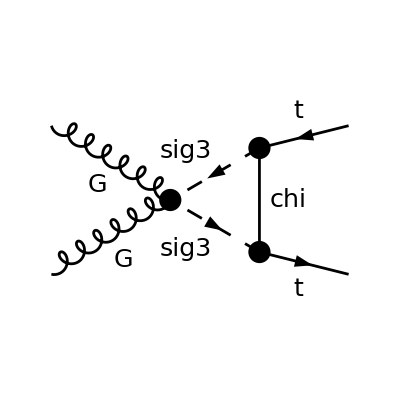

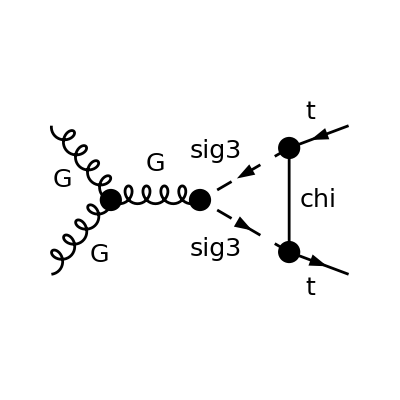

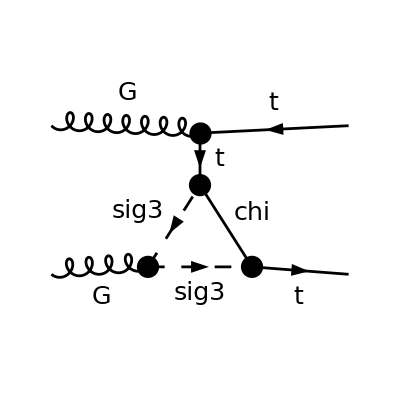

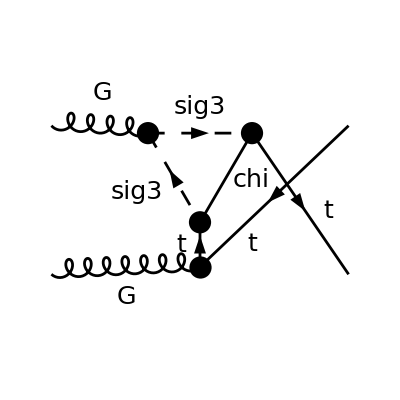

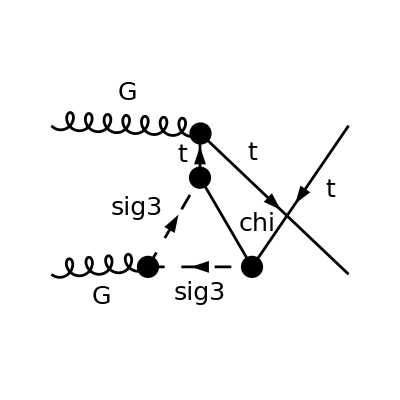

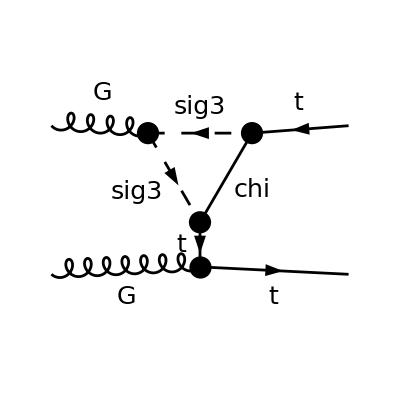

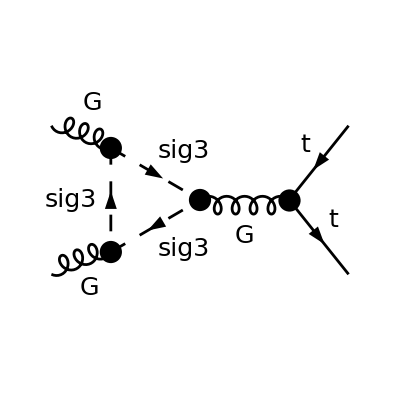

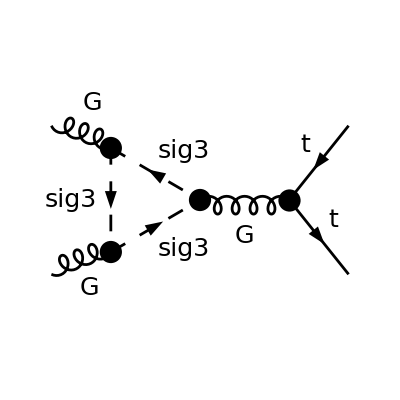

FeynArtsGraphics[SM-EFT][([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([])]

```mathematica
Paint[insSMEFT,ColumnsXRows->1,PaintLevel->{Classes},SheetHeader->nameSMEFT,Numbering->None,AutoEdit->True]
```

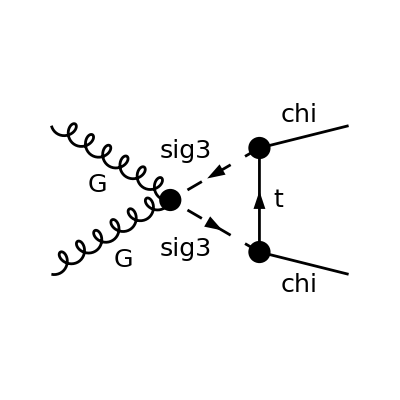

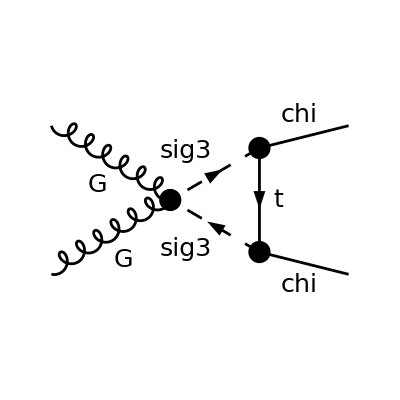

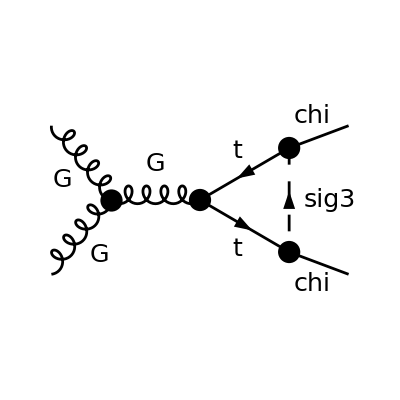

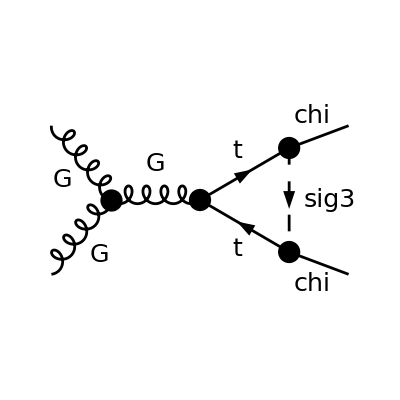

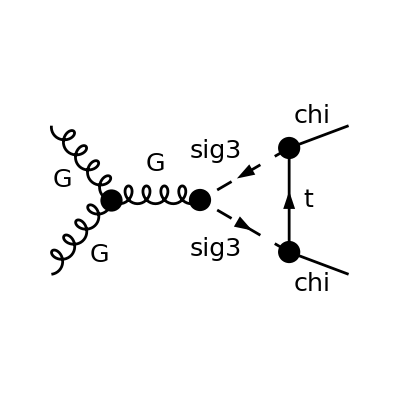

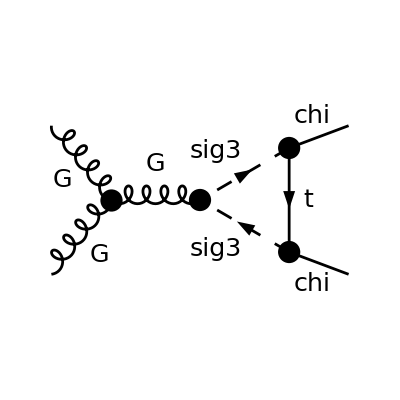

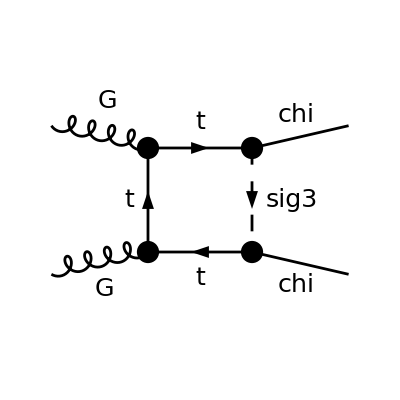

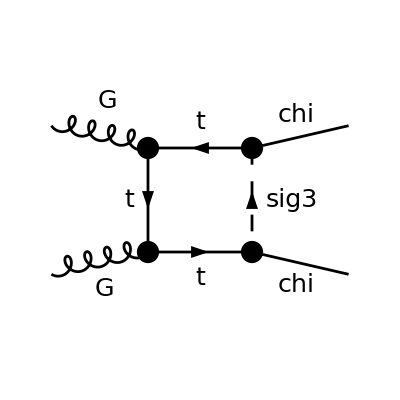

FeynArtsGraphics[DM-EFT][([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([])]

```mathematica
Paint[insDMEFT,ColumnsXRows->1,PaintLevel->{Classes},SheetHeader->nameDMEFT,Numbering->None,AutoEdit->True]
```

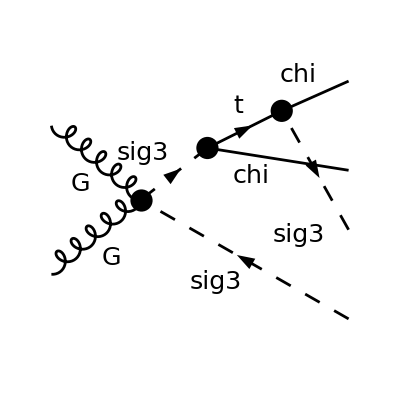

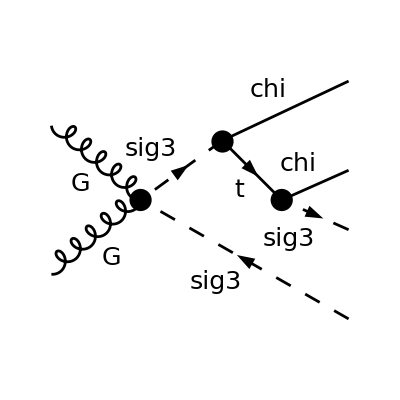

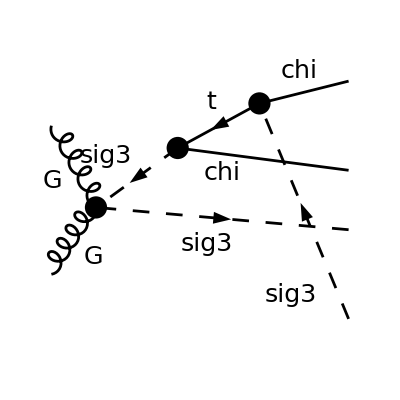

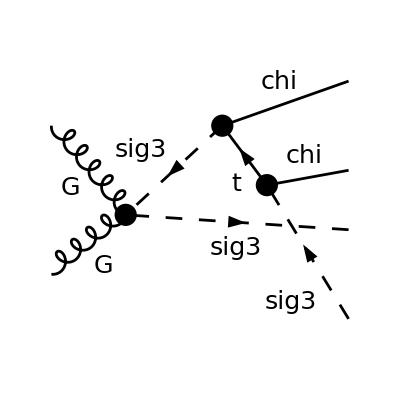

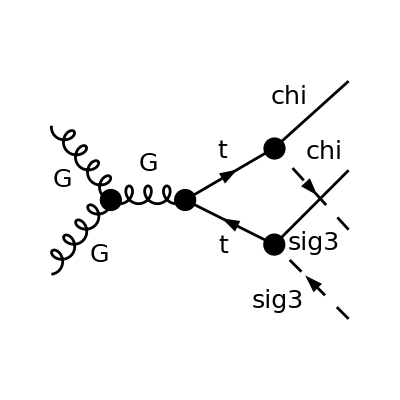

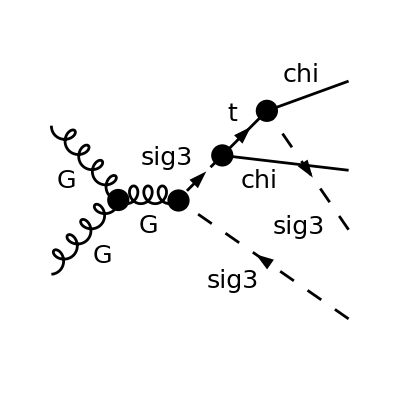

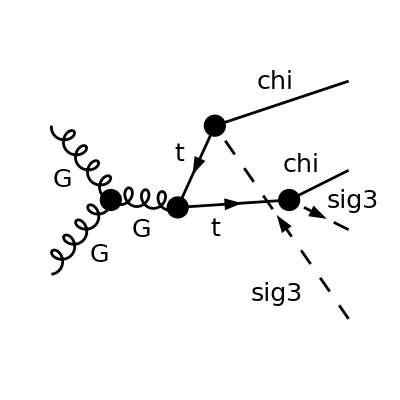

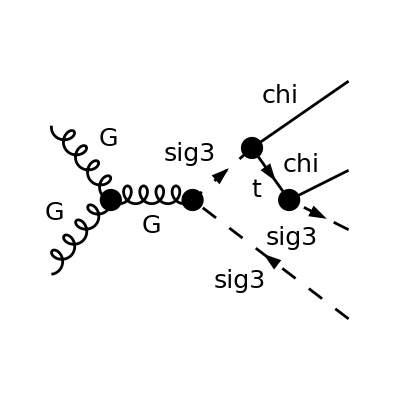

FeynArtsGraphics[SMS][([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([]),([])]

```mathematica
Paint[insSMS,ColumnsXRows->1,PaintLevel->{Classes},SheetHeader->nameSMS,Numbering->None,AutoEdit->True]
```